```mathematica
Clear["Global`*"]
data=Import[NotebookDirectory[]<>"ef.csv"][[10;;]];
ListPlot3D[data,ImageSize->Large,PlotRange->All]
```

-Graphics3D-

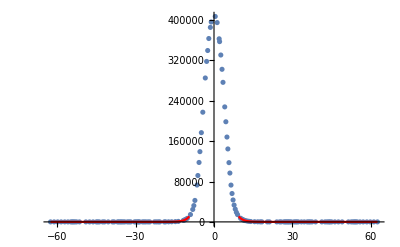

```mathematica
slice1=Select[data,Abs[#[[2]]]≤0.2&];
slice1=Transpose[{slice1[[All,1]],slice1[[All,3]]}];
slice1=DeleteDuplicatesBy[slice1,First];
ex=Interpolation[slice1,InterpolationOrder->3];
Show[ListPlot[slice1,PlotRange->All],Plot[ex[x],{x,Min[slice1[[All,1]]],Max[slice1[[All,1]]]},PlotStyle->Red]]
```

```mathematica
maxE=Max[slice1[[All,2]]];
diam=Abs[(x/.FindRoot[ex[x]==maxE/E^2,{x,-10}])-
(x/.FindRoot[ex[x]==maxE/E^2,{x,10}])]
```

13.8404